```mathematica
(*Wlog normalize gaussian to 1 via scaling, then only off by constant*)
Integrate[(1-x^2)*(1-1x^2)E^(-x^2/2)E^(-I x y)
,{x,-Infinity,Infinity}]
Integrate[(1-4x^2)E^(-x^2/2)E^(-I x y)
,{x,-Infinity,Infinity}]
Integrate[(1-a x^2)E^(-x^2/2)E^(-I x y)
,{x,-Infinity,Infinity}]
Integrate[(1-a x^2)(1-b x^2)E^(-x^2/2)E^(-I x y)
,{x,-Infinity,Infinity}]
```

ⅇ^(-y^2/2) √(2 π) (8-19 y^2+4 y^4)

ⅇ^(-y^2/2) √(2 π) (-3+4 y^2)

ⅇ^(-y^2/2) √(2 π) (1+a (-1+y^2))

ⅇ^(-y^2/2) √(2 π) (1+b (-1+y^2)+a (-1+y^2+b (3-6 y^2+y^4)))

ⅇ^(-y^2/2) √(2 π) (2-4 y^2+y^4)

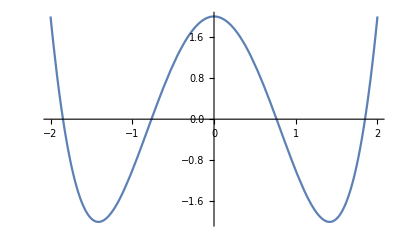

```mathematica
Integrate[(1-1*x^2)*(1-1*x^2)E^(-x^2/2)E^(-I x y)
,{x,-Infinity,Infinity}]

Plot[2-4 y^2+y^4,{y,-2,2}]
```

```mathematica
L[x_] = x^4 E^(-x^2/2)
```

ⅇ^(-x^2/2) x^4

ⅇ^(-y^2/2) √(2 π) (3-6 y^2+y^4)

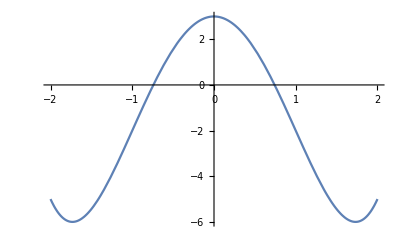

```mathematica
Integrate[L[x]E^(-I x y)
,{x,-Infinity,Infinity}]
Plot[3-6 y^2+y^4,{y,-2,2}]
```

```mathematica
Clear[n]
(*Density -> Chars*)

Integrate[x^(2)E^(-x^2/2)E^(-I x y),{x,-Infinity,Infinity}]

Integrate[x^(2* 2)E^(-x^2/2)E^(-I x y),{x,-Infinity,Infinity}]

Integrate[x^(2*3)E^(-x^2/2)E^(-I x y),{x,-Infinity,Infinity}]
```

-ⅇ^(-y^2/2) √(2 π) (-1+y^2)

ⅇ^(-y^2/2) √(2 π) (3-6 y^2+y^4)

-ⅇ^(-y^2/2) √(2 π) (-15+45 y^2-15 y^4+y^6)

ⅈ ⅇ^(-y^2/2) √(2 π) y (-3+y^2)

ⅇ^(-y^2/2) √(2 π)

-ⅈ ⅇ^(-y^2/2) √(2 π) y

```mathematica
(*Chars -> density*)
L[x_,n_] = 1/(Sqrt[2*Pi]) *x^(2n)* E^(-x^2/2)
dist = ProbabilityDistribution[L[x],{x,-Infinity,Infinity}]
```

(ⅇ^(-x^2/2) x^(2 n))/(√(2 π))

ProbabilityDistribution[x^4 ⅇ^(-x^2/2),{x,-∞,∞}]

```mathematica
Integrate[(3-6x^2+x^4)*E^(-x^2/2)E^(I x y),{x,-Infinity,Infinity}]
```

ⅇ^(-y^2/2) √(2 π) y^4

```mathematica
Integrate[1/Sqrt[a1]*L[x/Sqrt[a1],1]*1/Sqrt[1-a1]*L[(y-x)/Sqrt[1-a1],1],{x,-Infinity,Infinity}]
Integrate[1/Sqrt[a1]*L[x/Sqrt[a1],1]*1/Sqrt[1-a1]*L[(y-x)/Sqrt[1-a1],2],{x,-Infinity,Infinity}]
(*Would really like to be able to compute the symbolic integral*)
```

ConditionalExpression[(ⅇ^(-y^2/2) (y^2-(-1+a1) a1 (3-6 y^2+y^4)))/(√(2 π)), Re[a1]≥Re[a1^2]]

ConditionalExpression[(ⅇ^(-y^2/2) (-15 (-1+a1) a1^2+3 a1 (6+5 a1 (-4+3 a1)) y^2-(-1+a1) (1+5 a1 (-2+3 a1)) y^4+(-1+a1)^2 a1 y^6))/(√(2 π)), Re[a1]≥Re[a1^2]]

```mathematica
(*Is this convex?*)
Integrate[1/Sqrt[a1]*L[x/Sqrt[a1],2]*1/Sqrt[1-a1]*L[(y-x)/Sqrt[1-a1],2],{x,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(-y^2/2) (105 (-1+a1)^2 a1^2-30 (-1+a1) a1 (3+14 (-1+a1) a1) y^2+3 (1+10 (-1+a1) a1 (2+7 (-1+a1) a1)) y^4-2 (-1+a1) a1 (3+14 (-1+a1) a1) y^6+(-1+a1)^2 a1^2 y^8))/(√(2 π)), Re[a1]≥Re[a1^2]]

```mathematica
(*Key point is that the resulting density has exponent independent of a1,a2(even in inhomogeneous case) since we sum to 1. Understanding why this true would be very useful.*)
```

```mathematica
p22[y_,a1_] = 105 (-1+a1)^2 a1^2-30 (-1+a1) a1 (3+14 (-1+a1) a1) y^2+3 (1+10 (-1+a1) a1 (2+7 (-1+a1) a1)) y^4-2 (-1+a1) a1 (3+14 (-1+a1) a1) y^6+(-1+a1)^2 a1^2 y^8
ddp22[y_,a1_] = D[D[p22[y,a1],y],y]
f22[y_,a1_] = 1/(√(2 π))ⅇ^(-y^2/2) (105 (-1+a1)^2 a1^2-30 (-1+a1) a1 (3+14 (-1+a1) a1) y^2+3 (1+10 (-1+a1) a1 (2+7 (-1+a1) a1)) y^4-2 (-1+a1) a1 (3+14 (-1+a1) a1) y^6+(-1+a1)^2 a1^2 y^8)
ddf22[y_,a1_] =  D[D[f22[y,a1],y],y]
diff[y_,eps_] = f22[y,eps+1/2]-f22[y,1/2]
```

105 (-1+a1)^2 a1^2-30 (-1+a1) a1 (3+14 (-1+a1) a1) y^2+3 (1+10 (-1+a1) a1 (2+7 (-1+a1) a1)) y^4-2 (-1+a1) a1 (3+14 (-1+a1) a1) y^6+(-1+a1)^2 a1^2 y^8

-60 (-1+a1) a1 (3+14 (-1+a1) a1)+36 (1+10 (-1+a1) a1 (2+7 (-1+a1) a1)) y^2-60 (-1+a1) a1 (3+14 (-1+a1) a1) y^4+56 (-1+a1)^2 a1^2 y^6

1/(√(2 π))ⅇ^(-y^2/2) (105 (-1+a1)^2 a1^2-30 (-1+a1) a1 (3+14 (-1+a1) a1) y^2+3 (1+10 (-1+a1) a1 (2+7 (-1+a1) a1)) y^4-2 (-1+a1) a1 (3+14 (-1+a1) a1) y^6+(-1+a1)^2 a1^2 y^8)

1/(√(2 π))ⅇ^(-y^2/2) (-60 (-1+a1) a1 (3+14 (-1+a1) a1)+36 (1+10 (-1+a1) a1 (2+7 (-1+a1) a1)) y^2-60 (-1+a1) a1 (3+14 (-1+a1) a1) y^4+56 (-1+a1)^2 a1^2 y^6)-ⅇ^(-y^2/2) √(2/π) y (-60 (-1+a1) a1 (3+14 (-1+a1) a1) y+12 (1+10 (-1+a1) a1 (2+7 (-1+a1) a1)) y^3-12 (-1+a1) a1 (3+14 (-1+a1) a1) y^5+8 (-1+a1)^2 a1^2 y^7)-1/(√(2 π))ⅇ^(-y^2/2) (105 (-1+a1)^2 a1^2-30 (-1+a1) a1 (3+14 (-1+a1) a1) y^2+3 (1+10 (-1+a1) a1 (2+7 (-1+a1) a1)) y^4-2 (-1+a1) a1 (3+14 (-1+a1) a1) y^6+(-1+a1)^2 a1^2 y^8)+1/(√(2 π))ⅇ^(-y^2/2) y^2 (105 (-1+a1)^2 a1^2-30 (-1+a1) a1 (3+14 (-1+a1) a1) y^2+3 (1+10 (-1+a1) a1 (2+7 (-1+a1) a1)) y^4-2 (-1+a1) a1 (3+14 (-1+a1) a1) y^6+(-1+a1)^2 a1^2 y^8)

-(ⅇ^(-y^2/2) (105/16-(15 y^2)/4+(9 y^4)/8-y^6/4+y^8/16))/(√(2 π))+1/(√(2 π))ⅇ^(-y^2/2) (105 (-1/2+eps)^2 (1/2+eps)^2-30 (-1/2+eps) (1/2+eps) (3+14 (-1/2+eps) (1/2+eps)) y^2+3 (1+10 (-1/2+eps) (1/2+eps) (2+7 (-1/2+eps) (1/2+eps))) y^4-2 (-1/2+eps) (1/2+eps) (3+14 (-1/2+eps) (1/2+eps)) y^6+(-1/2+eps)^2 (1/2+eps)^2 y^8)

```mathematica
ListAnimate[Table[Plot[{ddp22[y,a1/10]},{y,0,1}],{a1,1,10}]]
ListAnimate[Table[Plot[{ddf22[y,a1/10]},{y,0,1}],{a1,1,10}]]
ListAnimate[Table[Plot[{diff[y,eps/100]},{y,0,10}],{eps,1,10}]]
(*So I seems convexity just breaks for higher atoms.*)
```